## Hexi—PS13—2025 - 03 - 25

### Exercises from EIWL3 Section 33

```mathematica
Head[ListPlot[{x,y}]]
```

Graphics

```mathematica
Times@@Range[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

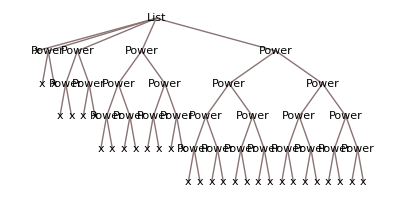

```mathematica
TreeForm[NestList[#^#&,x,4]]
```

```mathematica
Cases[Flatten[Table[i^2/(j^2+1),{i,20},{j,20}]],_Integer]
```

{2,8,5,18,32,50,20,10,2,72,98,45,128,17,162,200,80,40,8}

```mathematica
Graph[Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1]]
```

-Graphics-

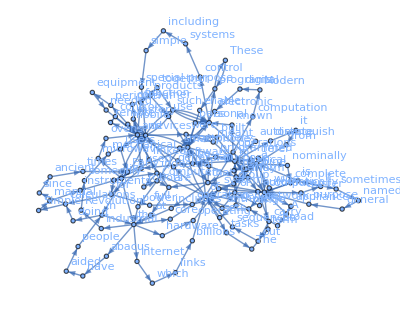

```mathematica
Graph[Rule@@@Partition[Take[TextWords[WikipediaData["computers"]],200],2,1],VertexLabels->Automatic]
```

```mathematica
f@@@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

### Exercises from EIWL3 Section 34

```mathematica
Values[KeySort[Counts[IntegerDigits[3^100]]]]
```

{7,9,9,5,1,5,4,7,1}

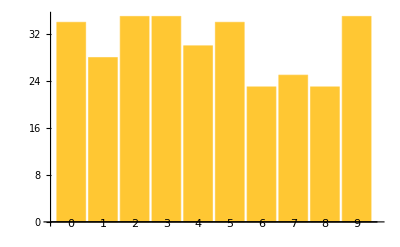

```mathematica
BarChart[Values[Counts[IntegerDigits[2^1000]]],ChartLabels->Range[0,9]]
```

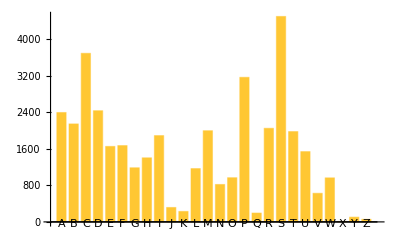

```mathematica
BarChart[Counts[ToUpperCase[StringTake[WordList[],1]]],ChartLabels->CharacterRange["A","Z"]]
```

```mathematica
Take[Sort[Counts[StringTake[WordList[],1]]],-5]
```

<|a→2393,d→2433,p→3168,c→3693,s→4499|>

```mathematica
(#q+#u)/Total[#]&@LetterCounts[WikipediaData["computers"]]//N
```

0.0338426

```mathematica
Keys[Take[Sort[Counts[TextWords[ExampleData[{"Text","AliceInWonderland"}]]]],-10]]
```

{it,in,Alice,was,of,she,to,a,and,the}